# VSIDM Transfer Cross Section

Ian Chaffey
09/17/2019
Updated: 12/11/2022

This notebook calculates the transfer cross section self-interaction dark matter with a mediator which yields an attractive or repulsive potential. This code is based on the algorithm described in https://arxiv.org/abs/1302.3898 and was used to create the self-interacting dark matter plots in https://arxiv.org/abs/1907.10217.

## Packages

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
```

## Radial Schrödinger Equation

### Equations

χ_l=r R_l	x=α_X m_X r	a=v/(2 α_X)	b=(α_X m_X)/m_ϕ

```mathematica
eqns[x_,xi_,a_,b_,l_,sign_]:={D[Subscript[χ, l][x],{x,2}]+(a^2 -l(l+1)/x^2-sign E^(-x/b)/x)Subscript[χ, l][x]==0,Subscript[χ, l][xi]==1,Subscript[χ, l]'[xi]==(l+1)/xi}
```

sign=-1 ⇒ Attractive
sign=+1 ⇒ Repulsive

```mathematica
χsol[x_,xi_,xm_,a_,b_,l_,sign_]:=Subscript[χ, l][x]/.NDSolve[eqns[x,xi,a,b,l,sign],Subscript[χ, l],{x,xi,xm},MaxSteps->200000,Method->"StiffnessSwitching"]//First
```

### Solution Range

```mathematica
xmax[a_,b_]:=b;
xmin[a_,b_,l_]:=Min[(l+1)/a,b];
max[a_,b_]:=100 xmax[a,b];
min[a_,b_,l_]:=xmin[a,b,l]/(1000.0 (l+1));
maxstep[a_,b_]:=max[a,b]/50
minstep[a_,b_,l_]:=min[a,b,l]/50;
```

## Phase Shift

```mathematica
β[xi_,xm_,a_,b_,l_,sign_]:= ((xm D[ Evaluate[χsol[x,xi,xm,a,b,l,sign]],x]/.{x->xm})/(Evaluate[χsol[x,xi,xm,a,b,l,sign]]/.{x->xm})-1)
δ[xi_?NumberQ,xm_?NumberQ,a_?NumberQ,b_?NumberQ,l_?NumberQ,sign_?NumberQ]:=If[xi>0,(ArcTan[(a xm (D[SphericalBesselJ[l,x],x]/.x->a xm)-Evaluate[β[xi,xm,a,b,l,sign]]SphericalBesselJ[l,a xm])/(a xm (D[SphericalBesselY[l,x],x]/.x->a xm )-Evaluate[β[xi,xm,a,b,l,sign]]SphericalBesselY[l,a xm])]),(ArcTan[(a xm (D[SphericalBesselJ[l,x],x]/.x->a xm)-Evaluate[β[10^-10,xm,a,b,l,sign]]SphericalBesselJ[l,a xm])/(a xm (D[SphericalBesselY[l,x],x]/.x->a xm)-(Evaluate[β[10^-10,xm,a,b,l,sign]])SphericalBesselY[l,a xm])])]
Δδ[xi_,xm_,a_,b_,l_,i_,sign_]:=Abs[(δ[xi-(i+1)minstep[a,b,l] ,xm+(i+1)maxstep[a,b],a,b,l,sign]-δ[xi+i minstep[a,b,l] ,xm+i maxstep[a,b],a,b,l,sign])]
δFinal[a_,b_,l_,sign_]:=Catch[Do[If[Δδ[min[a,b,l],max[a,b],a,b,l,i,sign]≤0.01Abs[δ[min[a,b,l]-i minstep[a,b,l],max[a,b]+i maxstep[a,b],a,b,l,sign]],Throw[δ[min[a,b,l]-(i+1)minstep[a,b,l],max[a,b]+(i+1)maxstep[a,b],a,b,l,sign]],Continue[]],{i,0,1500}]]
```

## Transfer Cross Section

We use natural units. The masses are taken as arguments in units of GeV and the resulting cross section has units GeV^-2.

The number of times the cross section is required to converge is determined by the ‘count’ inequality in σTFinal.

```mathematica
σT[α_,mx_,mphi_,v_,l_,sign_]:=(4 Pi)/((v mx)/2)^2(l+1)Sin[δFinal[v/(2 α),α mx/mphi,l+1,sign]-δFinal[v/(2 α),α mx/mphi,l,sign]]^2
σTFinal[α_,mx_,mphi_,v_,sign_]:=Catch[For[sigmal=σT[α,mx,mphi,v,0,sign];lmax=1;count=0,lmax≤2000,sigmal=sigmal+σT[α,mx,mphi,v,lmax,sign];lmax=lmax+1,If[σT[α,mx,mphi,v,lmax,sign]<0.01sigmal&&δFinal[v/(2 α),α mx/mphi,lmax,sign]<0.01,count=count+1,count=0];If[count≥3,Throw[sigmal+σT[α,mx,mphi,v,lmax,sign]],Continue[]]]]
vrange={1.,1.122,1.259,1.413,1.585,1.778,1.995,2.239,2.512,2.818,3.162,3.548,3.981,4.467,5.012,5.623,6.31,7.079,7.943,8.913,10.,11.22,12.589,14.125,15.849,17.783,19.953,22.387,25.119,28.184,31.623,35.481,39.811,44.668,50.119,56.234,63.096,70.795,79.433,89.125,100.,112.202,125.893,141.254,158.489,177.828,199.526,223.872,251.189,281.838,316.228,354.813,398.107,446.684,501.187,562.341,630.957,707.946,794.328,891.251,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.}/(3*10^5);
σTList[α_?NumberQ,mx_?NumberQ,mphi_?NumberQ,sign_?NumberQ]:=Table[{v,σTFinal[α,mx,mphi,v,sign]//Evaluate},{v,vrange}]
σTint[α_?NumberQ,mx_?NumberQ,mphi_?NumberQ,sign_?NumberQ]:=Interpolation[σTList[α,mx,mphi,sign]]
```

For large values the dark matter relative velocity, the cross section may fail to converge. In this case the closed form results for the classical cross sections may be used to extrapolate the curve as is done in https://arxiv.org/abs/1302.3898.

### Test Loop for Debugging

Iterates over the max angular momentum mode  ℓ_max.

```mathematica
Loop[α_,mx_,mphi_,v_,sign_]:=Catch[For[sigmal=σT[α,mx,mphi,v,0,sign];lmax=1;count=0,lmax≤2000,sigmal=sigmal+σT[α,mx,mphi,v,lmax,sign];lmax=lmax+1,Print[((5.06 10^13)^-2)/(1.78 10^-24)(sigmal+σT[α,mx,mphi,v,lmax,sign])/mx];If[σT[α,mx,mphi,v,lmax,sign]<0.01sigmal&&δFinal[v/(2 α),α mx/mphi,lmax,sign]<0.01,count=count+1,count=0];If[count≥1,Throw[sigmal+σT[α,mx,mphi,v,lmax,sign]],Continue[]]]]
```

### Interpolated Cross Sections

```mathematica
SetDirectory[NotebookDirectory[]];
```

The interpolating functions will be made in the current directory.

#### Dark Photon Model

Cross section for the dark photon model presented in https://arxiv.org/abs/1508.03339. In this model the dark matter abundance is asymmetric resulting in a purely repulsive force.

```mathematica
sigmadarkphoton = σTint[1/137,15,0.017,1];
```

```mathematica
sigmadarkphoton>>"sigmadarkphoton.m"
```

Velocity Averaged Cross Section

```mathematica
σvavedarkphoton[vave_]:=4 Pi NIntegrate[v^2/(Pi/2 vave)^3 sigmadarkphoton[v]v  Exp[-4/Pi v^2/vave^2],{v,1/(3*10^5),10^4/(3*10^5)}]
```

#### VSIDM Model

Cross section for the VSIDM model presented in https://arxiv.org/abs/1907.10217. In this mode the dark matter abundance is symmetric resulting in an attractive and repulsive force.

Naming convention for interpolating functions: "bvalue-b-mX-mphi .m" with no dashes in the actual file name.

Repulsive Potential

```mathematica
sigmaVSIDMrep=σTint[1.35*10^-6,0.06,0.000095,1];
sigmaVSIDMrep>>"sigma00085b60MeV95keVrep.m";
```

Attractive Potential

```mathematica
sigmaVSIDMatt=σTint[1.35*10^-6,0.06,0.000095,-1];
sigmaVSIDMatt>>"sigma00085b60MeV95keVratt.m";
```

The total cross section is the average of both the attractive and repulsive cases

```mathematica
sigmaVSIDMave[v_]:=(sigmaVSIDMrep[v]+sigmaVSIDMatt[v])/2
```

Velocity Averaged Cross Section

```mathematica
σvaveVSIDM[vave_]:=4 Pi NIntegrate[v^2/(Pi/2 vave)^3 sigmaVSIDMave[v]v  Exp[-4/Pi v^2/vave^2],{v,1/(3*10^5),10^4/(3*10^5)}]
```

#### Example Cross Sections

Attractive Potential

```mathematica
sigmab1att = σTint[0.01,100,1,-1]
```

InterpolatingFunction[…]

```mathematica
sigmab1dot53att = σTint[0.01,100,1/1.53,-1]
```

InterpolatingFunction[…]

```mathematica
sigmab1dot68att = σTint[0.01,100,1/1.68,-1]
```

InterpolatingFunction[…]

```mathematica
sigmab3dot13att = σTint[0.01,100,1/3.13,-1]
```

InterpolatingFunction[…]

```mathematica
sigmab4dot52att = σTint[0.01,100,1/4.52,-1]
```

InterpolatingFunction[…]

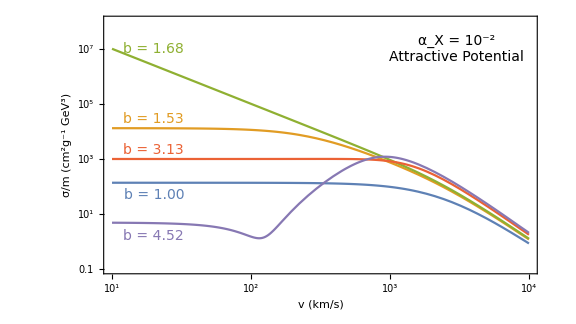

```mathematica
Plot[{((5.06 10^13)^-2)/(1.78 10^-24)(100)^3 sigmab1att[v/(3*10^5)]/100,((5.06 10^13)^-2)/(1.78 10^-24)(100)^3 sigmab1dot53att[v/(3*10^5)]/100,((5.06 10^13)^-2)/(1.78 10^-24)(100)^3 sigmab1dot68att[v/(3*10^5)]/100,((5.06 10^13)^-2)/(1.78 10^-24)(100)^3 sigmab3dot13att[v/(3*10^5)]/100,((5.06 10^13)^-2)/(1.78 10^-24)(100)^3 sigmab4dot52att[v/(3*10^5)]/100},{v,10,10000},ScalingFunctions->{"Log10","Log10"},Frame->True,FrameLabel-> {"v (km/s)","σ/m (cm^2g^-1 GeV^3)"},FrameStyle-> Directive[Black,14],ImageSize->Large, AspectRatio->9/16,PlotRangePadding->{{None,None},Automatic},PlotRange->{0.1,10^8},Epilog->{Text[Style["b = 1.00",14,ColorData[97,1]],{Log10[20],Log10[50]}],Text[Style["b = 1.53",14,ColorData[97,2]],{Log10[20],Log10[27000]}],Text[Style["b = 1.68",14,ColorData[97,3]],{Log10[20],Log10[10^7]}],Text[Style["b = 3.13",14,ColorData[97,4]],{Log10[20],Log10[2000]}],Text[Style["b = 4.52",14,ColorData[97,5]],{Log10[20],Log10[1.5]}],Text[Style["α_X = 10^-2\nAttractive Potential",14,Black],{Log10[3000],Log10[10^7]}]}]
```